### Old code of mine

#### 10-15-2024: Using actual spin-flip matrix elements - setting θi, ϕi = θf, ϕf (looks like I was using a single random θi, ϕi for each NDIS before) (hops = 40k, NDIS = 15k)

NDIS = 60k
max hops = 20k

```mathematica
dataTable=Take[Import["Documents/RESEARCH/spin simulations/2024-Fall/Quantum 1 Target MT/out1MT_s0.dat"],21];
ff=FindFit[dataTable, A Exp[-γ*t],{A,γ},t]
```

{A→1.00405,γ→0.0261824}

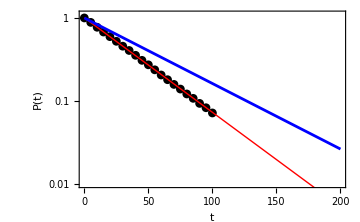

```mathematica
Show[ ListLogPlot[{dataTable},PlotRange-> {{0.0,200},{0.01,1.1}}, Joined->False,PlotStyle->{{Black,PointSize->0.0175},{Red,PointSize->0.0175}}],LogPlot[{ A Exp[-γ*t]/.ff, Exp[-0.018158307050237445*t]},{t,0,200},PlotRange->All, PlotStyle->{{Red, Thick},{Blue}, {Red, Thick, Dashed}}], FrameStyle->{{Black,Thick},{Black,Thick}, None, None},FrameTicksStyle->Directive[Black,18], Frame->{True, True, False, False},FrameLabel->{"t","P(t)"},LabelStyle->Directive[Black,22]]
```

```mathematica
(32 π *0.001^2 *1.07/1*10^-3)/(9 6.58*10^-7)*1
```

0.0181642

```mathematica
(γ/.ff)/((32 π *0.001^2 *1.07/1*10^-3)/(9 6.58*10^-7)*1)
```

1.44143

```mathematica
((γ/.ff)/((32 π *0.001^2 *1.07/1*10^-3)/(9 6.58*10^-7)*1))^-1
```

0.693755